```mathematica
ASTOR PRIETO DEHGHANPOUR
```

# Pràctica 10: Grafs amb Mathematica

En aquesta pràctica aprendrem a dibuixar grafs de varies maneres en Mathematica, així com diferents funcions que defineixen grafs especials i que estan implementades en la llibreria DiscreteMath`.

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Dibuixem un graf amb cinc vèrtexs i tal que, del primer vèrtex, sortiran arestes cap a tots els altres vèrtexs i del tercer vèrtexs una aresta cap al quart. Ho farem utilitzant la funció FromUnorderedPairs[]que construeix el graf a partir de la llista d'arestes. Aquesta llista està formada per parells {a,b} indicant que hi ha una aresta unint els vèrtexs a i b.

{{3,2},{3,1},{3,4},{3,5},{1,4}}

⁃Graph:<5,5,Undirected>⁃

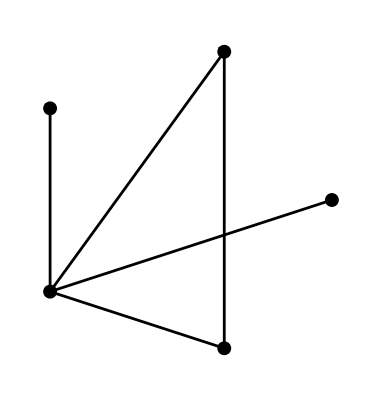

```mathematica
Ar={{3,2},{3,1},{3,4},{3,5} ,{1,4}}
G=FromUnorderedPairs[Ar]
ShowLabeledGraph[G]
```

Podem dibuixar el mateix graf sense les etiquetes dels vertexs fent

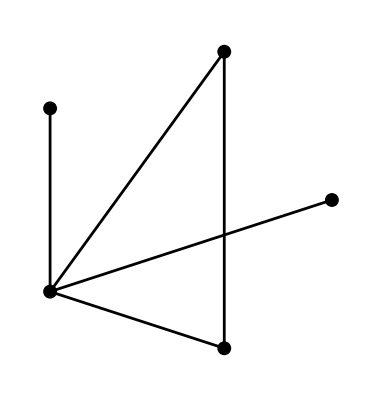

```mathematica
ShowGraph[G]
```

Donat un graf podem recuperar la llista d'arestes amb la instrucció Edges:

```mathematica
Edges[G]
```

{{2,3},{1,3},{3,4},{3,5},{1,4}}

Hi ha molts tipus de grafs importants que tenen nom propi, com per exemple els grafs complets K_n, els grafs cíclics C_n, els grafs estrella, els grafs roda, el graf buit d'ordre n, etc. Aquests grafs es poden generar amb Mathematica de la manera següent:

```mathematica
ShowLabeledGraph[CompleteGraph[7]]
```

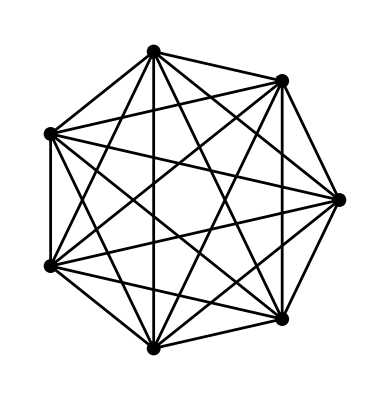

```mathematica
ShowLabeledGraph[Cycle[7]]
```

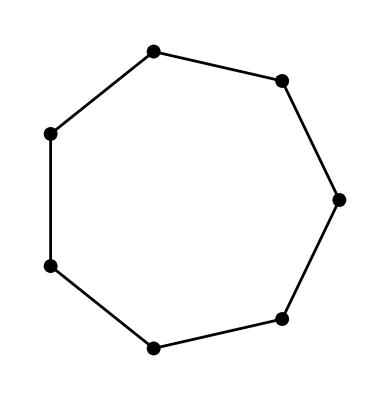

```mathematica
ShowLabeledGraph[Star[8]]
```

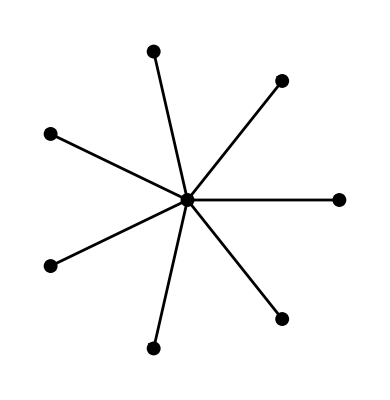

```mathematica
ShowLabeledGraph[Wheel[10]]
```

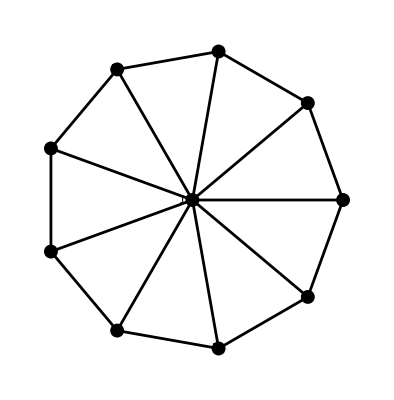

```mathematica
ShowLabeledGraph[EmptyGraph[7]]
```

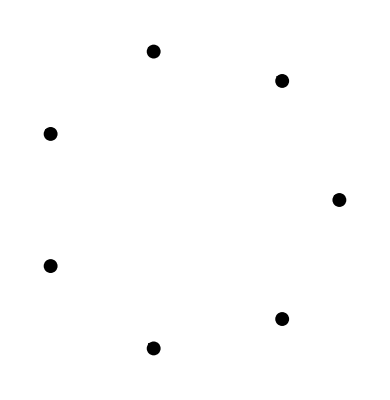

#### Exercici 1

Dibuixeu i trobeu les llistes d'arestes del graf complet K_5, el graf cíclic C_6 i el graf roda de 7 vèrtexs.

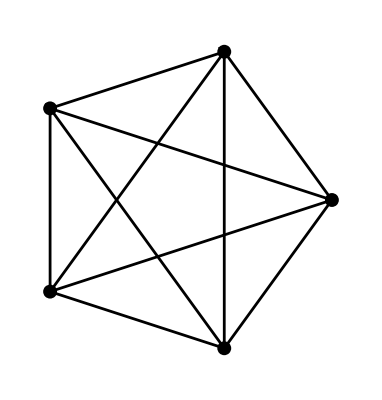

```mathematica
ShowLabeledGraph[CompleteGraph[5]]
```

```mathematica
Edges[CompleteGraph[5]]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

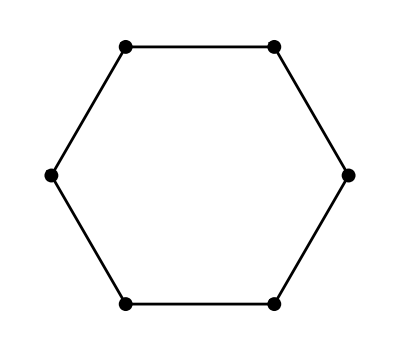

```mathematica
ShowLabeledGraph[Cycle[6]]
```

```mathematica
Edges[Cycle[6]]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{1,6}}

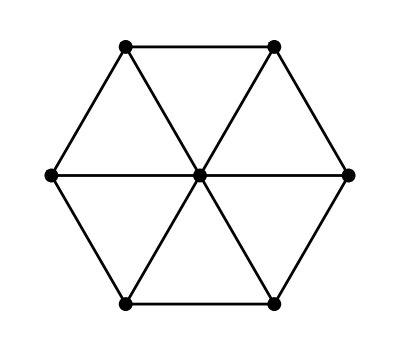

```mathematica
ShowLabeledGraph[Wheel[7]]
```

```mathematica
Edges[Wheel[7]]
```

{{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,2},{2,3},{3,4},{4,5},{5,6},{1,6}}

Els veïns d'un vèrtex v són aquells vèrtexs que estan units a v directament per una aresta. La llista dels veïns de tots els vèrtexs s'anomena Taula d'adjacències del graf i es pobtenir amb la funció ToAdjacencyLists[]

```mathematica
T = ToAdjacencyLists[G]
```

{{3,4},{3},{1,2,4,5},{1,3},{3}}

Donada una taula d'adjacències podem recuperar el graf amb la funció FromAdjacencyLists[].

```mathematica
FromAdjacencyLists[T]
```

⁃Graph:<5,5,Undirected>⁃

#### Exercici 2

Trobeu la taula d'adjacències del graf complet d'ordre 5 i construïu el graf següent a partir de la seva taula d'adjacències.

```mathematica
ToAdjacencyLists[CompleteGraph[5]]
```

{{2,3,4,5},{1,3,4,5},{1,2,4,5},{1,2,3,5},{1,2,3,4}}

A més a més estan implementades moltes funcions que permeten treballar còmodament amb grafs. Per exemple és possible unir grafs, multiplicar grafs, colapsar vèrtexs, esborrar arestes, ... Per exemple, la funció AddEdge[G,{a,b}] afegeix al graf G una aresta entre els vèrtexs a i b.

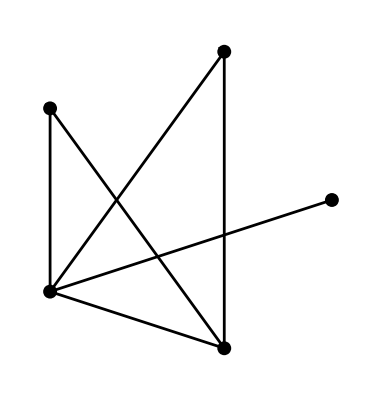

```mathematica
G1=AddEdge[G,{2,4}];
ShowLabeledGraph[G1]
```

⁃Graph:<7,5,Undirected>⁃

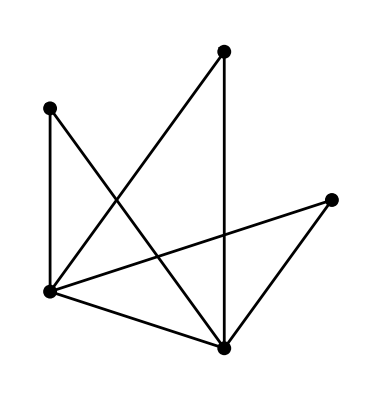

```mathematica
G2=AddEdge[G1,{4, 5}]
ShowLabeledGraph[G2]
```

### Camins i cicles

Una qüestió interessant que codifica molts problemes de la vida real és veure quins recorreguts es poden fer sobre les arestes d'un graf donat. Un camí o recorregut és una successió ordenada de vèrtexos {v_1,v_2,...,v_n} tal que {v_i,v_(i+1)} és una aresta.Un cicle és un camí tancat (v_1=v_n) tal que tots els vèrtexs que el componen (llevat del primer i l'últime) són diferents.

Un cicle hamiltonià és un cicle que passa per tots els vèrtexs del graf; és a dir un recorregut tancat que passa una vegada i només una per cada vèrtex del graf. Comprovem si existeix algun cicle hamiltonià en el graf G.

```mathematica
HamiltonianQ[G]
```

False

#### Exercici per trametre

- Comproveu que el graf de l'exercici 2 és Hamiltonià i trobeu un cicle hamiltonià.

```mathematica
HamiltonianQ[CompleteGraph[5]]
```

True

- Quins dels següents grafs són hamiltonians?

```mathematica
A1 = {{1,2},{1,5},{1,6},{2,3},{2,7},{3,4},{3,8},{4,5},{4,9},{5,10},{6,11},{6, 12},{7, 11},{7,15},{8,15},{8,14},{9,14},{9,13},{10,12},{10,13},{11,16},{12,17},{13,18},{14,19},{15,20},{16,17},{17,18},{18,19},{19,20},{20,16}}
Graph1 = FromUnorderedPairs[A1]
HamiltonianQ[Graph1]
```

{{1,2},{1,5},{1,6},{2,3},{2,7},{3,4},{3,8},{4,5},{4,9},{5,10},{6,11},{6,12},{7,11},{7,15},{8,15},{8,14},{9,14},{9,13},{10,12},{10,13},{11,16},{12,17},{13,18},{14,19},{15,20},{16,17},{17,18},{18,19},{19,20},{20,16}}

⁃Graph:<30,20,Undirected>⁃

True

```mathematica
A2={{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}
Graph2 = FromUnorderedPairs[A2]
HamiltonianQ[Graph2]
```

{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}

⁃Graph:<9,6,Undirected>⁃

True

```mathematica
A3={ {1,2},{1,3},{1,4}}
Graph3=FromUnorderedPairs[A2]
HamiltonianQ[Graph3]
```

{{1,2},{1,3},{1,4}}

⁃Graph:<9,6,Undirected>⁃

True

```mathematica
A4={{1,2},{1,3},{1,4},{1,5},{1,9},{2,3},{2,7},{2,8},{2,9},{3,5},{3,6},{3,7},{4,5},{4,9},{4,10},{4,12},{5,6},{5,12},{6,7},{6,11},{6,12},{7,8},{7,11},{8,9},{8,10},{8,11}}
Graph4 = FromUnorderedPairs[A4]
HamiltonianQ[Graph4]
```

{{1,2},{1,3},{1,4},{1,5},{1,9},{2,3},{2,7},{2,8},{2,9},{3,5},{3,6},{3,7},{4,5},{4,9},{4,10},{4,12},{5,6},{5,12},{6,7},{6,11},{6,12},{7,8},{7,11},{8,9},{8,10},{8,11}}

⁃Graph:<26,12,Undirected>⁃

True

```mathematica
A5={{1,4},{1,5},{2,4},{2,5},{2,6},{3,4},{3,5},{4,6},{5,6}}
Graph5 = FromUnorderedPairs[A5]
HamiltonianQ[Graph5]
```

{{1,4},{1,5},{2,4},{2,5},{2,6},{3,4},{3,5},{4,6},{5,6}}

⁃Graph:<9,6,Undirected>⁃

False

```mathematica
A6={{
```

```mathematica
A7={{1,2},{1,9},{2,9},{3,4},{3,9},{4,9},{5,6},{5,9},{6,9},{7,8},{7,9},{8,9}}
Graph7=FromUnorderedPairs[A7]
HamiltonianQ[Graph7]
```

{{1,2},{1,9},{2,9},{3,4},{3,9},{4,9},{5,6},{5,9},{6,9},{7,8},{7,9},{8,9}}

⁃Graph:<12,9,Undirected>⁃

False

```mathematica
A8={{1,2},{1,4},{1,5},{1,7},{2,3},{2,5},{2,6},{2,7},{2,9},{3,4},{3,6},{3,7},{3,9},{4,7},{4,10},{5,6},{5,8},{6,7},{6,8},{6,9},{7,9},{8,9},{8,10},{9,10}}
Graph8=FromUnorderedPairs[A8]
HamiltonianQ[Graph8]
```

{{1,2},{1,4},{1,5},{1,7},{2,3},{2,5},{2,6},{2,7},{2,9},{3,4},{3,6},{3,7},{3,9},{4,7},{4,10},{5,6},{5,8},{6,7},{6,8},{6,9},{7,9},{8,9},{8,10},{9,10}}

⁃Graph:<24,10,Undirected>⁃

True

```mathematica
A9={{1,5},{1,8},{2,5},{2,6},{3,6},{3,7},{4,7},{4,8},{5,6},{5,8},{6,7},{7,8}}
Graph9=FromUnorderedPairs[A9]
HamiltonianQ[Graph9]
```

{{1,5},{1,8},{2,5},{2,6},{3,6},{3,7},{4,7},{4,8},{5,6},{5,8},{6,7},{7,8}}

⁃Graph:<12,8,Undirected>⁃

True

```mathematica
<<RESPOSTES>>
```

```mathematica
G1 = Si
G2 = Si
G3 = Si
G4 = Si
G5 = No
G6 = Si
G7 = No
G8 = No
G9 = No
```